## Bose-Hubbard model simulation

```mathematica
SetDirectory[NotebookDirectory[]];
```

### General definitions

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
HBose[t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
HBose[t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]],{j,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j)]],{j,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperature *)
Subscript[β, val]=3/5;
```

### Static energy-energy correlations

```mathematica
BondEnergyOp[j_,t_,U_,M_,L_]:=-t(KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]])+U/4(KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1]),SparseIdentityMatrix[(M+1)^(L-j)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1]),SparseIdentityMatrix[(M+1)^(L-j-1)]])
```

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_energy_static/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
(* read simulation results from disk *)
```

```mathematica
Subscript[ee, corr]=Partition[Import[Subscript[fn, import]<>"_ee_corr.dat","Real64"],Subscript[L, val]-1]
Dimensions[%]
```

{{1.29802,0.0592822,0.176,0.18718},{0.0592748,1.40755,0.0356971,0.175898},{0.176,0.0356995,1.40759,0.0591832},{0.18718,0.175898,0.0591857,1.29861}}

{4,4}

```mathematica
(* not exactly symmetric for nearest neighbors *)
Subscript[ee, corr]-Transpose[Subscript[ee, corr]]//MatrixForm
Norm[%]
```

(0. | 7.46427×10^-6 | 2.498×10^-16 | 3.05311×10^-16
-7.46427×10^-6 | 0. | -2.34755×10^-6 | 8.04912×10^-16
-2.498×10^-16 | 2.34755×10^-6 | 0. | -2.5026×10^-6
-3.05311×10^-16 | -8.04912×10^-16 | 2.5026×10^-6 | 0.)

7.8643×10^-6

```mathematica
Subscript[e, avr,A]=Import[Subscript[fn, import]<>"_e_avr_A.dat","Real64"]
Subscript[e, avr,B]=Import[Subscript[fn, import]<>"_e_avr_B.dat","Real64"]
```

{-0.433464,-0.403364,-0.403359,-0.433216}

{-0.433464,-0.403364,-0.403359,-0.433216}

```mathematica
(* should agree *)
Norm[Subscript[e, avr,A]-Subscript[e, avr,B]]
```

1.2573×10^-15

```mathematica
(* cumulant *)
Subscript[ee, cum]=Subscript[ee, corr]-KroneckerProduct[Subscript[e, avr,A],Subscript[e, avr,B]];
```

```mathematica
(* reference calculation *)
```

```mathematica
Comm[A_,B_]:=A.B-B.A
```

```mathematica
(* Hamiltonian and neighboring bond energy operators do not commute *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],H,i=2,j=3},H=HBose[tH,U,μ,M,L];{Norm[Comm[BondEnergyOp[i,tH,U,M,L],H]],Norm[Comm[BondEnergyOp[i,tH,U,M,L],BondEnergyOp[j,tH,U,M,L]]]}]
```

{√Root[-4050+15505 #1-387 #1^2+2 #1^3&,3],√(1/2 (95+2 √811))}

```mathematica
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],H,expβH},H=N[HBose[tH,U,μ,M,L]];expβH=MatrixExp[-β H];Subscript[ee, corr,ref]=Table[Tr[expβH.BondEnergyOp[i,tH,U,M,L].BondEnergyOp[j,tH,U,M,L]]/Tr[expβH],{i,L-1},{j,L-1}];Subscript[e, avr,ref]=Table[Tr[expβH.BondEnergyOp[i,tH,U,M,L]]/Tr[expβH],{i,L-1}];Subscript[ee, cum,ref]=Subscript[ee, corr,ref]-KroneckerProduct[Subscript[e, avr,ref],Subscript[e, avr,ref]];];
```

```mathematica
(* check symmetry *)
Norm[Subscript[ee, corr,ref]-Transpose[Subscript[ee, corr,ref]]]
```

1.13946×10^-16

```mathematica
(* compare *)
Norm[Subscript[ee, corr]-Subscript[ee, corr,ref]]
Norm[Subscript[ee, cum]-Subscript[ee, cum,ref]]
Norm[Subscript[e, avr,A]-Subscript[e, avr,ref]]
Norm[Subscript[e, avr,B]-Subscript[e, avr,ref]]
```

0.000421603

0.000489254

0.00018112

0.00018112

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]]<>", β="<>ToString[N[Subscript[β, val]]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

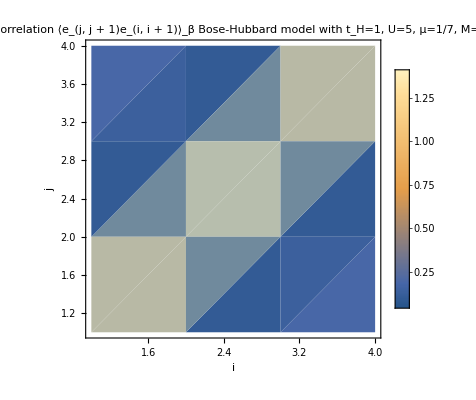

```mathematica
ListDensityPlot[Subscript[ee, corr],PlotLegends->Automatic,FrameLabel->{"i","j"},PlotLabel->"energy-energy correlation ⟨e_(j, j + 1)e_(i, i + 1)⟩_β\n"<>Subscript[plot, label]]
Export[Subscript[fn, export]<>"ee_corr_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

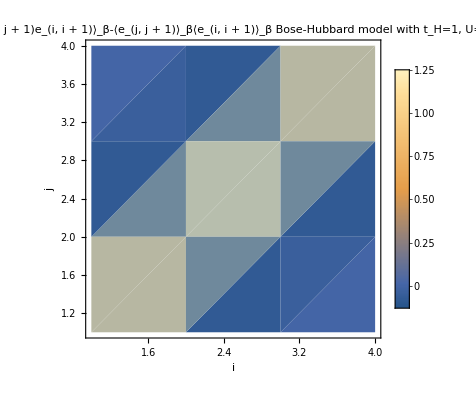

```mathematica
ListDensityPlot[Subscript[ee, cum],PlotLegends->Automatic,FrameLabel->{"i","j"},PlotLabel->"energy-energy cumulant ⟨e_(j, j + 1)e_(i, i + 1)⟩_β-⟨e_(j, j + 1)⟩_β⟨e_(i, i + 1)⟩_β\n"<>Subscript[plot, label]]
Export[Subscript[fn, export]<>"ee_cumulant_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

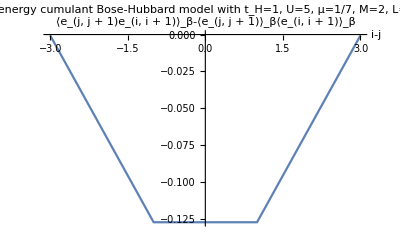

```mathematica
ListLinePlot[Transpose[{Range[-(Subscript[L, val]-2),Subscript[L, val]-2,2],Diagonal[Reverse/@Subscript[ee, cum]]}],AxesLabel->{"i-j","⟨e_(j, j + 1)e_(i, i + 1)⟩_β-⟨e_(j, j + 1)⟩_β⟨e_(i, i + 1)⟩_β"},PlotLabel->"energy-energy cumulant\n"<>Subscript[plot, label]]
Export[Subscript[fn, export]<>"ee_cut_L"<>ToString[Subscript[L, val]]<>".pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H/2) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff_beta.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.